```mathematica
ClearAll["Global`*"]
```

```mathematica
r=√(x^2+y^2+z^2);
X={x,y,z};
Γ={{0,1,0},{0,0,0},{0,0,0}};
Id={{1,0,0},{0,1,0},{0,0,1}};
Γ'=Transpose[Γ];
XX=Outer[Times,X,X];
Γdoubledot=Total[Total[Table[Γ[[i]]  XX[[i]],{i,1,3}]]];
e=1/2(Γ+Γ');
o= 1/2(Γ-Γ');
e2=Total[Total[Table[e[[i]]  e[[i]],{i,1,3}]]];
o2=Total[Total[Table[o[[i]]  o[[i]],{i,1,3}]]];
ϵ=-0.5;
De=1;
n={0,1,0};
```

## Velocity Streamlines for a Passive Sphere

```mathematica
u0=Γ.X-(e.X)/r^5-(5(X.e.X)X)/(2 r^5)(1-1/r^2);
P1=VectorDensityPlot[{u0[[1]]/.z->0,u0[[2]]/.z->0},{x,-5,5},{y,-5,5},VectorColorFunction->"Aquamarine",ColorFunction->"PigeonTones",StreamPoints->Fine,PlotRange->All,FrameLabel->{"x","y"},Epilog->{Red,Disk[{0,0},1]},AspectRatio->1,PlotLabel->Style["Passive Sphere in Shear flow",Bold,14],ImageSize->350];
u1=(1+ϵ)(-5/14 (22/r^7-35/r^6+13/r^5) (e.e).X-5/14 (14/r^10-77/r^9+105/r^8-43/r^7+1/r^5) X((e.X).(e.X))+5/4 (-10/r^10+22/r^9-15/r^8+3/r^7)( Γdoubledot(e.X))-5/8 (-40/r^12+99/r^11-80/r^10+21/r^9)(Γdoubledot^2 X)+5/84 (-33/r^7+70/r^6-39/r^5+2/r^3)(e2 X));
P2=VectorDensityPlot[{u1[[1]]/.z->0,u1[[2]]/.z->0},{x,-5,5},{y,-5,5},VectorColorFunction->"Aquamarine",ColorFunction->"AvocadoColors",StreamPoints->Fine,PlotRange->All,FrameLabel->{"x","y"},Epilog->{Cyan,Disk[{0,0},1]},AspectRatio->1,PlotLabel->Style["Plane of Shear(z=0)",Bold,14],ImageSize->350];
u=u0+De(u1);
ufinal=u/.z->0;
P3=VectorDensityPlot[{ufinal[[1]],ufinal[[2]]},{x,-4,4},{y,-4,4},VectorColorFunction->"Aquamarine",ColorFunction->"AvocadoColors",StreamPoints->Fine,PlotRange->All,FrameLabel->{"x","y"},Epilog->{Cyan,Disk[{0,0},1]},AspectRatio->1,PlotLabel->Style["Effects of Weak Viscoelasticity ",Bold,14],ImageSize->350];
```

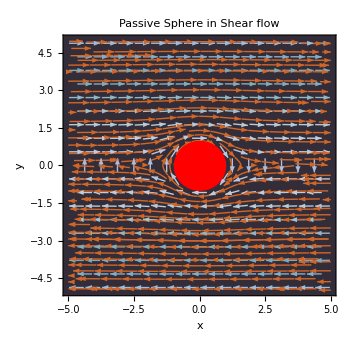
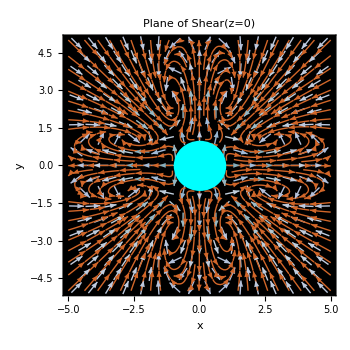
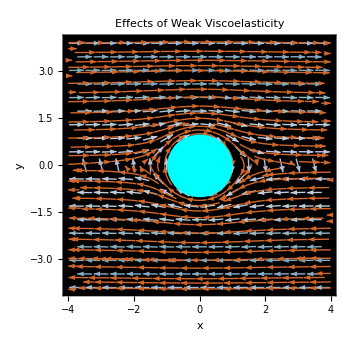

```mathematica
Row[{P1,P2,P3}]
```

```mathematica
(*Define the effective velocity field in the z=0 plane*)uVec0=u0/. z->0;
ux01=uVec0[[1]]/.{x->x[t],y->y[t]};
ux02=uVec0[[2]]/.{x->x[t],y->y[t]};
initials0=Table[{-0.75+i1*0.05,-0.75-i1*0.05},{i1,-6.5,6.5}];
(*Solve the trajectory ODE starting from (x,y)=(-0.75,-0.75)*)
(*Manipulate trajectory with time*)
p0=Manipulate[Show[Table[Module[{sol,x0,y0},x0=pt[[1]];y0=pt[[2]];
sol=NDSolve[{x'[t]==ux01,y'[t]==ux02,x[0]==x0,y[0]==y0},{x,y},{t,0,tmax}];
ParametricPlot[Evaluate[{x[t],y[t]}/. sol],{t,0,tmax},PlotStyle->Black]],{pt,initials}],PlotRange->{{-2,2},{-2,2}},AxesLabel->{"x","y"},Epilog->{Red,PointSize[Medium]},PlotLabel->Style["Spiral Trajectories (De=0.1, ε=-0.5) up to t="<>ToString[tmax],Bold,14]],{{tmax,100,"Time"},10,1000,10}];
```

```mathematica
(*Define effective velocity field*)
uVec=u/. z->0;
ux1=uVec[[1]]/. {x->x[t],y->y[t]};
ux2=uVec[[2]]/. {x->x[t],y->y[t]};

(*Initial conditions list*)
initials=Table[{-0.75+i*0.05,-0.75-i*0.05},{i,-6,6}];

(*Manipulate trajectory with time*)
p1=Manipulate[Show[Table[Module[{sol,x0,y0},x0=pt[[1]];y0=pt[[2]];
sol=NDSolve[{x'[t]==ux1,y'[t]==ux2,x[0]==x0,y[0]==y0},{x,y},{t,0,tmax}];
ParametricPlot[Evaluate[{x[t],y[t]}/. sol],{t,0,tmax},PlotStyle->Black]],{pt,initials}],PlotRange->{{-4,4},{-4,4}},AxesLabel->{"x","y"},Epilog->{Red,PointSize[Medium]},PlotLabel->Style["Spiral Trajectories (De=0.1, ε=-0.5) up to t="<>ToString[tmax],Bold,14]],{{tmax,100,"Time"},10,1000,10}];
Row[{p0,p1}]
```